```mathematica
Manipulate[DiscretePlot[(Fa!Fb!)/((Fa+Fb+1)!p0^Fa(1-p0)^Fb),{Fa,1,20}], {p0,0.1,1},{Fb,1,20}]
```

```mathematica
Manipulate
```

```mathematica
3!
```

6

```mathematica
BaseForm[6,2]
```

110_2

```mathematica
a=RandomInteger[{1,200}]
```

132

```mathematica
n=50;p=1/2;L=Table[Log[(a!(n-a)!)/((n+1)!(p)^a(1-p)^(n-a))],{i,0,50}];
```

```mathematica
Mean[L]//N
```

-1.74502

```mathematica
a
```

```mathematica
Table[RandomInteger[{0,200}]!(1-RandomInteger[{0,200}])!
```

```mathematica
RandomInteger[{0,200}]
```

172

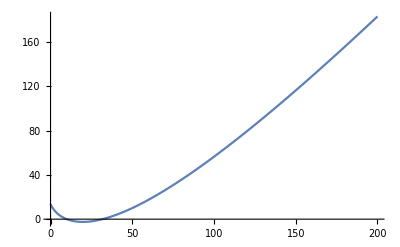

```mathematica
Fb=100;p0=1/6;Plot[Log[(Fa!Fb!)/((Fa+Fb+1)!p0^Fa(1-p0)^Fb)],{Fa,0,200}]
```

```mathematica
P(e=1|p=1)= P(e=1,a=0|p=1)+P(e=1,a=1|p=1)
```

```mathematica
π2=1-π1;π1=0.6;μ1=i/20;μ2=j/20;
```

```mathematica
T=Table[π1/σ1 Exp[(-(x-μ1)^2)/(2 σ1^2)]+π2/σ2 Exp[(-(x-μ2)^2)/(2 σ2^2)],{i,0,2},{j,0,2}];
```

```mathematica
T
```

{{(0.6 ⅇ^(-x^2/(2 σ1^2)))/σ1+(0.4 ⅇ^(-x^2/(2 σ2^2)))/σ2,(0.6 ⅇ^(-x^2/(2 σ1^2)))/σ1+(0.4 ⅇ^(-(-1/20+x)^2/(2 σ2^2)))/σ2,(0.6 ⅇ^(-x^2/(2 σ1^2)))/σ1+(0.4 ⅇ^(-(-1/10+x)^2/(2 σ2^2)))/σ2},{(0.6 ⅇ^(-(-1/20+x)^2/(2 σ1^2)))/σ1+(0.4 ⅇ^(-x^2/(2 σ2^2)))/σ2,(0.6 ⅇ^(-(-1/20+x)^2/(2 σ1^2)))/σ1+(0.4 ⅇ^(-(-1/20+x)^2/(2 σ2^2)))/σ2,(0.6 ⅇ^(-(-1/20+x)^2/(2 σ1^2)))/σ1+(0.4 ⅇ^(-(-1/10+x)^2/(2 σ2^2)))/σ2},{(0.6 ⅇ^(-(-1/10+x)^2/(2 σ1^2)))/σ1+(0.4 ⅇ^(-x^2/(2 σ2^2)))/σ2,(0.6 ⅇ^(-(-1/10+x)^2/(2 σ1^2)))/σ1+(0.4 ⅇ^(-(-1/20+x)^2/(2 σ2^2)))/σ2,(0.6 ⅇ^(-(-1/10+x)^2/(2 σ1^2)))/σ1+(0.4 ⅇ^(-(-1/10+x)^2/(2 σ2^2)))/σ2}}

```mathematica
Manipulate[Plot[{(0.6 ⅇ^(-x^2/(2 σ1^2)))/σ1+(0.4 ⅇ^(-x^2/(2 σ2^2)))/σ2,(0.6 ⅇ^(-(-1+x)^2/(2 σ1^2)))/σ1+(0.4 ⅇ^(-(-2+x)^2/(2 σ2^2)))/σ2},{x,0,3}],{σ1,1,3},{σ2,1,3}]
```

```mathematica
pkIxth=(pxkIth pk)/pxIth=(pxkIth pk)/(Subscript[Σ, k] pxkth)
```

```mathematica
(x-m1)^2-(x-m2)^2//Simplify
```

(m1-m2) (m1+m2-2 x)

```mathematica
p1/(p1 Exp[-(x-m1)^2]/Exp[-(x-m1)^2]+p2 Exp[-(x-m2)^2]/Exp[-(x-m1)^2])//Simplify
```

p1/(p1+ⅇ^((m1-m2) (m1+m2-2 x)) p2)

```mathematica
p2/(p1 Exp[-(x-m1)^2]/Exp[-(x-m2)^2]+p2 Exp[-(x-m2)^2]/Exp[-(x-m2)^2])//Simplify
```

p2/(ⅇ^(-(m1-m2) (m1+m2-2 x)) p1+p2)

```mathematica
Clear[pk1,pk2]
```

```mathematica
Solve[{pk1==p1/(p1+ⅇ^((m1-m2) (m1+m2-2 x)) p2),pk2==p2/(ⅇ^(-(m1-m2) (m1+m2-2 x)) p1+p2)},{p1,p2}]
```

{}

```mathematica
Solve[pk1==p1/(p1+ⅇ^((m1-m2) (m1+m2-2 x)) p2),p2]
```

{{p2→-(ⅇ^(-(m1-m2) (m1+m2-2 x)) p1 (-1+pk1))/pk1}}

```mathematica
p2/(ⅇ^(-(m1-m2) (m1+m2-2 x)) p1+p2)/.{p2->-(ⅇ^(-(m1-m2) (m1+m2-2 x)) p1 (-1+pk1))/pk1}//Simplify
```

```mathematica
Solve[1-pk1==pk2,
```

```mathematica
m1
```

m1

```mathematica
x
```

x

```mathematica
L=Log[p1/(√(2π σ^2))Exp[(-(x-μ1)^2)/(2 σ^2)]+p2/(√(2π σ^2))Exp[(-(x-μ2)^2)/(2 σ^2)]]
```

Log[(ⅇ^(-(x-μ1)^2/(2 σ^2)) p1)/(√(2 π) √(σ^2))+(ⅇ^(-(x-μ2)^2/(2 σ^2)) p2)/(√(2 π) √(σ^2))]

```mathematica
D[L,μ1]//FullSimplify
```

(p1 (x-μ1))/((p1+ⅇ^(((μ1-μ2) (-2 x+μ1+μ2))/(2 σ^2)) p2) σ^2)

```mathematica
(ⅇ^(-(x-μ1)^2/(2 σ^2)) p1 (x-μ1))/(√(2 π) (σ^2)^(3/2))/L
```

(ⅇ^(-(x-μ1)^2/(2 σ^2)) p1 (x-μ1))/(√(2 π) (σ^2)^(3/2) ((ⅇ^(-(x-μ1)^2/(2 σ^2)) p1)/(√(2 π) √(σ^2))+(ⅇ^(-(x-μ2)^2/(2 σ^2)) p2)/(√(2 π) √(σ^2))))

```mathematica
L1=Table[i/16,{i,32}]
```

{1/16,1/8,3/16,1/4,5/16,3/8,7/16,1/2,9/16,5/8,11/16,3/4,13/16,7/8,15/16,1,17/16,9/8,19/16,5/4,21/16,11/8,23/16,3/2,25/16,13/8,27/16,7/4,29/16,15/8,31/16,2}

```mathematica
L2=Table[4+i/16,{i,32}]
```

{65/16,33/8,67/16,17/4,69/16,35/8,71/16,9/2,73/16,37/8,75/16,19/4,77/16,39/8,79/16,5,81/16,41/8,83/16,21/4,85/16,43/8,87/16,11/2,89/16,45/8,91/16,23/4,93/16,47/8,95/16,6}

```mathematica
x=Join[L1,L2]
```

{1/16,1/8,3/16,1/4,5/16,3/8,7/16,1/2,9/16,5/8,11/16,3/4,13/16,7/8,15/16,1,17/16,9/8,19/16,5/4,21/16,11/8,23/16,3/2,25/16,13/8,27/16,7/4,29/16,15/8,31/16,2,65/16,33/8,67/16,17/4,69/16,35/8,71/16,9/2,73/16,37/8,75/16,19/4,77/16,39/8,79/16,5,81/16,41/8,83/16,21/4,85/16,43/8,87/16,11/2,89/16,45/8,91/16,23/4,93/16,47/8,95/16,6}

```mathematica
Mean[L1]
```

33/32

```mathematica
√Variance[x]
```

(√(493/7))/4

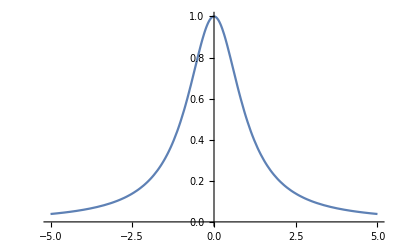

```mathematica
Plot[1/(1+(x)^2),{x,-5,5}]
```

```mathematica
∫_(-∞)^∞ x/(1+(x)^2)ⅆx
```

Integrate::idiv: Integral of x/1 + x^2 does not converge on {-∞, ∞}.

∫_(-∞)^∞ x/(1+x^2)ⅆx

```mathematica
∫_-a^a x^2/(1+(x)^2)ⅆx
```

ConditionalExpression[2 a-2 ArcTan[a],Re[a]≠0||-1<Im[a]<0||0<Im[a]<1]

```mathematica
∫_-100^100 x^2/(1+(x)^2)ⅆx
```

```mathematica
200-2 ArcTan[100]//N
```

196.878

```mathematica
1/(√(3π)Gamma[3/2]/Gamma[2])∫_(-∞)^∞ x^2/((1+(x)^2/3)^2)ⅆx
```

3

```mathematica
s=3;
```

```mathematica
1/(√(2π s^2))Exp[-x^2/(2 s^2)]
```

```mathematica
∫_(-∞)^∞ x^2/(√(2π s^2))Exp[-x^2/(2 s^2)]ⅆx
```

9

```mathematica
1/(√(2π s^2))//N
```

0.132981

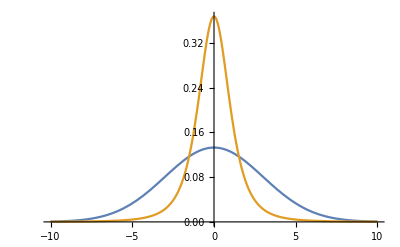

```mathematica
Plot[{1/(√(2π s^2))Exp[-x^2/(2 s^2)],1/(√(3π)Gamma[3/2]/Gamma[2])1/((1+(x)^2/3)^2)},{x,-10,10}]
```

```mathematica
GD[x_]:=1/(Gamma[c]s)(x/s)^(c-1)Exp[(- x)/s]
```

```mathematica
Solve[D[GD[x],x]==0,x]
```

{{x→-s+c s}}

```mathematica
∫_0^∞ x GD[x]ⅆx
```

ConditionalExpression[((1/s)^c s^(1+c) Gamma[1+c])/Gamma[c],Re[s]>0&&Re[c]>-1]

```mathematica
(s^2 Gamma[2+c])/Gamma[c]-((s Gamma[1+c])/Gamma[c])^2//Simplify
```

(s^2 (-Gamma[1+c]^2+Gamma[c] Gamma[2+c]))/Gamma[c]^2

```mathematica
μ=c s;σ^2=c s^2;
```

```mathematica
(s^2 (-Gamma[1+c]^2+Gamma[c] Gamma[2+c]))/Gamma[c]^2/.c->3
```

3 s^2

```mathematica
(s Gamma[1+c])/Gamma[c]/.c->3
```

3 s

```mathematica
ConditionalExpression[(1/s)^c s^c,Re[s]>0&&Re[c]>0]/.c->2
```

ConditionalExpression[1,Re[s]>0]

```mathematica
Clear[μ,σ]
```

```mathematica
G[x_]:=(1/(√(2π)σ))Exp[(-(x-μ)^2)/(2 σ^2)]
```

```mathematica
Solve[D[G[x],x]==0,x]
```

{{x→μ}}

```mathematica
Log[G[x]]//Simplify
```

Log[(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)]

```mathematica
GDN=(1/(Gamma[c]s))^N∏_(n=1)^N (Subscript[x, n]/s)^(c-1)Exp[∑_(n=1)^N (- Subscript[x, n])/s]
```

(1/(s Gamma[c]))^N ∏_(n=1)^N ⅇ^(∑_(n=1)^N -x_n/s) (x_n/s)^(-1+c)

```mathematica
xn={-27.02,3.57,8.191,9.898,9.603,9.945,10.056}
```

{-27.02,3.57,8.191,9.898,9.603,9.945,10.056}

```mathematica
Mean[xn]
```

3.46329

```mathematica
∫_(-∞)^∞ Exp[(-N(μ-x)^2)/(2 σ^2)]ⅆμ
```

ConditionalExpression[(√(2 π))/(√(N/σ^2)),Re[N/σ^2]≥0]

```mathematica
(1/(Gamma[0.1] 10^0.1))^7(1/(2π))^(7/2)∫_0^∞ σ^0.1 Exp[(-(x-μ)^2)/(2 σ^2)+σ/10]ⅆσ
```

4.54973×10^-11 ∫_0^∞ ⅇ^(-(x-μ)^2/(2 σ^2)+σ/10) σ^0.1ⅆσ

```mathematica
∫_0^∞ σ^c Exp[(-(x-μ)^2)/(2 σ^2)-σ/s]ⅆσ
```

```mathematica
ConditionalExpression[11.976796597153522 HypergeometricPFQ[{},{-0.050000000000000044,0.44999999999999996},-1/800 (x-μ)^2]-(1.2220697972757049 HypergeometricPFQ[{},{1.55,0.5},-1/800 (x-μ)^2])/((1/(x-μ)^2)^0.55)-(0.47443725266903375 HypergeometricPFQ[{},{2.05,1.4999999999999998},-1/800 (x-μ)^2])/((1/(x-μ)^2)^1.05),Re[(x-μ)^2]>0]/.x->10
```

ConditionalExpression[11.9768 HypergeometricPFQ[{},{-0.05,0.45},-1/800 (10-μ)^2]-(1.22207 HypergeometricPFQ[{},{1.55,0.5},-1/800 (10-μ)^2])/((1/(10-μ)^2)^0.55)-(0.474437 HypergeometricPFQ[{},{2.05,1.5},-1/800 (10-μ)^2])/((1/(10-μ)^2)^1.05),Re[(10-μ)^2]>0]

```mathematica
Assuming[Re[(x-μ)^2]>0,∫_0^∞ σ^0.1 Exp[-(x-μ)^2/(2 σ^2)]Exp[-σ/10]ⅆσ]
```

```mathematica
Clear[plot]
```

```mathematica
plot[x_]:=11.976796597153522 HypergeometricPFQ[{},{-0.050000000000000044,0.44999999999999996},-1/800 (x-μ)^2]-(1.2220697972757049 HypergeometricPFQ[{},{1.55,0.5},-1/800 (x-μ)^2])/((1/(x-μ)^2)^0.55)-(0.47443725266903375 HypergeometricPFQ[{},{2.05,1.4999999999999998},-1/800 (x-μ)^2])/((1/(x-μ)^2)^1.05)
```

```mathematica
HypergeometricPFQ[{},{-0.050000000000000044,0.44999999999999996},-1/800 (0.1)^2]
```

1.00056

```mathematica
∫σ^0.1 Exp[-(x-μ)^2/(2 σ^2)]Exp[σ/10]ⅆσ
```

∫ⅇ^(-(x-μ)^2/(2 σ^2)+σ/10) σ^0.1ⅆσ

```mathematica
∫σ^0.1 Exp[σ]ⅆσ
```

-(1. σ^1.1 Gamma[1.1,-1. σ])/(-1. σ)^1.1

```mathematica
Clear[x,μ]
```

```mathematica
s=10;c=0.1;x=12.1;μ=10;
```

```mathematica
x=-20;
```

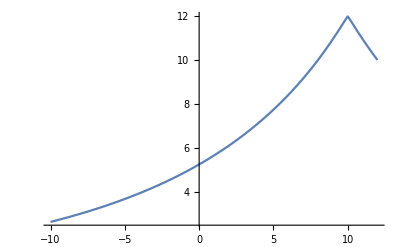

```mathematica
Plot[plot[10],{μ,-10,12}]
```

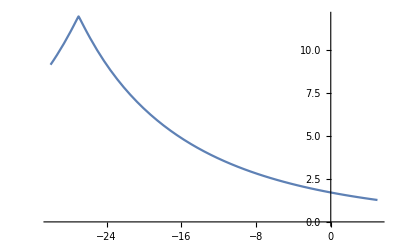

```mathematica
Plot[plot[-27],{μ,-30,5}]
```

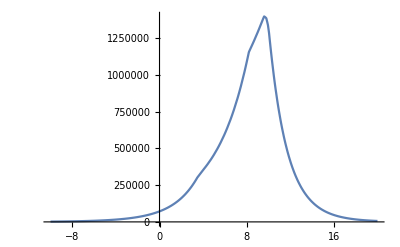

```mathematica
Plot[plot[-27]plot[3.6]plot[8.2]plot[9.8]plot[9.6]plot[9.95]plot[10.05],{μ,-10,20}]
```

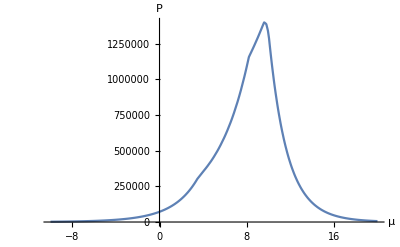

```mathematica
Show[%67,AxesLabel->{HoldForm[μ],HoldForm[P]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

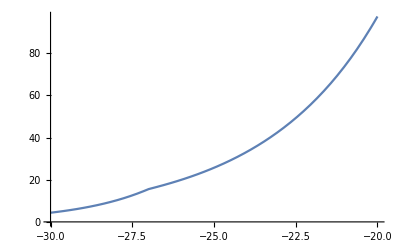

```mathematica
Plot[plot[-27]plot[3.6]plot[8.2]plot[9.8]plot[9.6]plot[9.95]plot[10.05],{μ,-30,-20}]
```

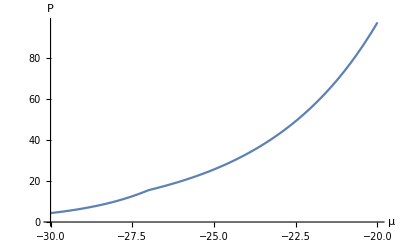

```mathematica
Show[%64,AxesLabel->{HoldForm[μ],HoldForm[P]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
∫_-20^30 plot[-27]plot[3.6]plot[8.2]plot[9.8]plot[9.6]plot[9.95]plot[10.05]ⅆμ
```

$Aborted

```mathematica
(1/(Gamma[0.1] 10^0.1))^7(1/(2π))^(7/2)
```

4.54973×10^-11

```mathematica
1/(√(2π))//N
```

0.398942

```mathematica
Gamma[0.1]
```

9.51351

```mathematica
P(s|m)= (P(m|s)P(s))/(P(m))
```

```mathematica
1/(Gamma[r]/(r!))Exp[-λ] λ^r/(r!)1/λ
```

```mathematica
post=(ⅇ^-λ λ^(-1+r))/Gamma[r]
```

(ⅇ^-λ λ^(-1+r))/Gamma[r]

```mathematica
∫_0^∞ Exp[-λ] λ^r/(r!)1/λ ⅆλ
```

ConditionalExpression[Gamma[r]/(r!),Re[r]>0]

```mathematica
Solve[D[(ⅇ^-λ λ^(-1+r))/Gamma[r],λ]==0,λ]
```

{{λ→-1+r}}

```mathematica
(ⅇ^-λ λ^(-1+r))/Gamma[r]/.{λ->-1+r}//Simplify
```

```mathematica
(ⅇ^(1-r) (-1+r)^(-1+r))/((r-1)!)//Simplify
```

```mathematica
L=Log[(ⅇ^-λ λ^(-1+r))/Gamma[r]]
```

Log[(ⅇ^-λ λ^(-1+r))/Gamma[r]]

```mathematica
D[D[L,λ],λ]//Simplify
```

(1-r)/λ^2

```mathematica
c=1/(r-1)
```

1/(-1+r)

```mathematica
PolyGamma
```

```mathematica
1/((-1+r) ((-1+r)!)^2)(((-1+r)!)^2+(-1+r) Gamma[r]^2 PolyGamma[0,r]^2-(-1+r) (-1+r)! Gamma[r] (PolyGamma[0,r]^2+PolyGamma[1,r]))
```

```mathematica
Gamma[4]
```

6

```mathematica
PolyGamma[1,3]
```

-5/4+π^2/6

```mathematica
c
```

1/9

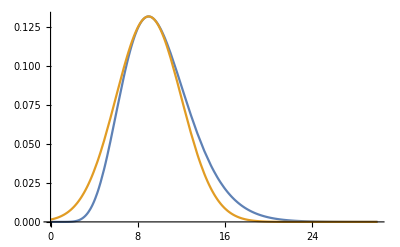

```mathematica
r=10;Plot[{Exp[-λ] λ^r/(r!)1/λ r,(ⅇ^(1-r) (-1+r)^(-1+r))/((r-1)!)Exp[-c/2(λ-(r-1))^2]},{λ,0,30}]
```

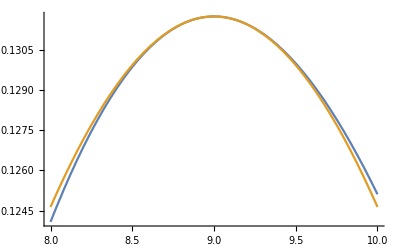

```mathematica
r=10;Plot[{Exp[-λ] λ^r/(r!)1/λ r,(ⅇ^(1-r) (-1+r)^(-1+r))/((r-1)!)Exp[-c/2(λ-(r-1))^2]},{λ,8,10}]
```

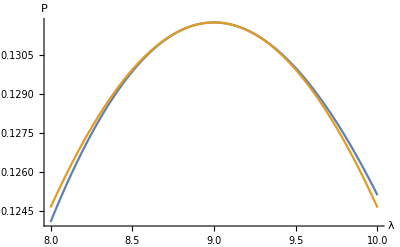

```mathematica
Show[%39,AxesLabel->{HoldForm[λ],HoldForm[P]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Clear[r]
```

```mathematica
{Exp[-λ] λ^r/(r!)r}/.λ->Exp[x]
```

{(ⅇ^(-ⅇ^x) (ⅇ^x)^r r)/(r!)}

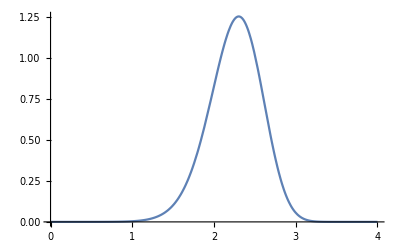

```mathematica
r=10;Plot[(ⅇ^(-ⅇ^x) (ⅇ^x)^r r)/(r!),{x,0,4}]
```

```mathematica
Exp[-(x-μ)^2/(2 σ^2)]
```